Post (μ:13.1098)

Post (δ:2.55934)

Post (σ:0.62508)

5.29208/((3+2.55934 (-13.1098+x)^2)^2)

Piecewise[{{1/2 BetaRegularized[1.17217/(1.17217+(-13.1098+x)^2),3/2,1/2], x≤13.1098}, {1/2 (1+BetaRegularized[(-13.1098+x)^2/(1.17217+(-13.1098+x)^2),1/2,3/2]), True}}]

ConditionalExpression[Piecewise[{{13.1098-1.08267 √(-1+1/InverseBetaRegularized[2 x,3/2,1/2]), 0<x<1/2}, {13.1098, x==1/2}, {13.1098+1.08267 √(-1+1/InverseBetaRegularized[2 (1-x),3/2,1/2]), 1/2<x<1}, {-∞, x≤0}, {∞, True}}],0≤x≤1]

13.1098

0.5

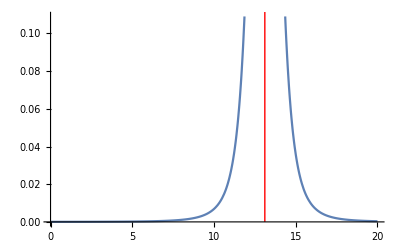

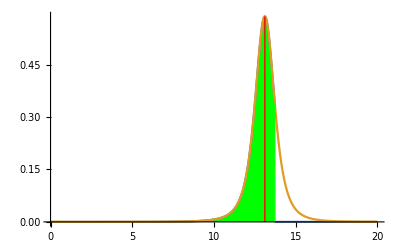

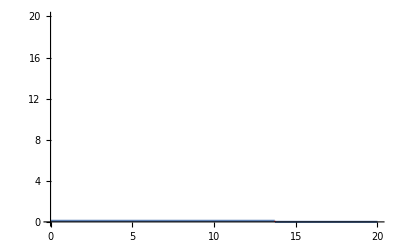

{-∞,15.2862}

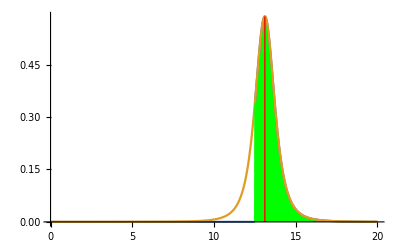

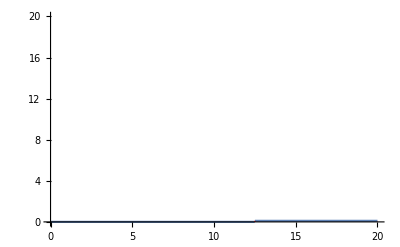

{10.9333,∞}

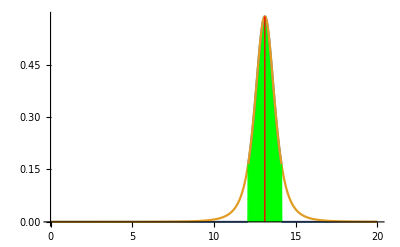

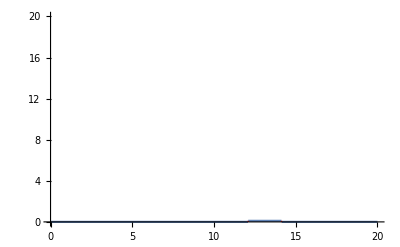

{10.2715,15.9481}

```mathematica
(*Prior for ukjent σ posterior*)
μpre:= 14;
σpre := 6;
(*Observasjons data*)
(*Skriv inn antall måle data*)
n := 4;
(*Snittet til måledatene*)
snitt := 13.1;
(*Skriv inn utvalgsvariansen*)
Sy := 1.257;
(*Mellom regniger*)
δdata = n/Sy^2;
δpost = 1/σpre + δdata;

(*Posterior*)
δpost := δpre+δdata;
μpost := δpre/δpost*μpre+δdata/δpost*snitt;
σpost := 1/Sqrt[δpost];

(*Velg størrelsen på konfidensintervallet*)
konfint := 0.98;
(*For endringer på intervallet som vises når data tegnes opp*)
Nedre := 0.0;
Ovre := 20.0;

Post μ:μpost
Post δ:δpost
Post σ:σpost


Temp:=StudentTDistribution[μpost,σpost,n-1];
f[t_]:=PDF[Temp,t];
F[t_]:=CDF[Temp,t];
Ff[t_]:=InverseCDF[Temp,t];

theInterval[t_,start_,end_]:=UnitStep[t-Ff[start]] (1-UnitStep[t-Ff[1-end]])
cF[t_,start_,end_]:=f[t] theInterval[t,start,end];
ciPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,Nedre,Ovre},PlotRange->All,Filling->{1->{Axis,{Green}},2->{{1},{White}}}]
ciIPlot[start_,end_,range_]:=Plot[0.1 theInterval[x,start,end],{x,Nedre,Ovre},PlotRange->{Nedre,Ovre},Filling->{1->{Axis,{Red}}}]
cendPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,0,1},PlotRange->All,Filling->{1->{Axis,{White}},2->{{1},{Red}}}]
f[x]
F[x]
Ff[x]
Mean[Temp]
F[Mean[Temp]]//N
Show[Plot[f[t],{t,Nedre,Ovre}],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]]

(*Venstre intervall*)

Show[
ciPlot[0,0.2,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[0,0.2,0.03]
{Ff[0.0],Ff[konfint]}

(*Høyre intervall*)
Show[
ciPlot[0.2,0,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[0.2,0,0.03]
{Ff[1-konfint],Ff[1]}

(*Symetriskkonfidensintervall om μ*)
Show[
ciPlot[F[Mean[Temp]]-0.4,0.6-F[Mean[Temp]],0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[F[Mean[Temp]]-0.4,0.6-F[Mean[Temp]],0.03]
{Ff[F[Mean[Temp]]-konfint/2],Ff[F[Mean[Temp]]+konfint/2]}
```